```mathematica
<<coproduct.m
```

```mathematica
countLyndonBasis[n_,alphabet_]:=Block[{m=Length[alphabet],d=Divisors@n},Plus@@(MoebiusMu[n/d]*m^d/n)]
generateLyndonBasis[{n__},alphabet_]:=Block[{fullBasis=generateLyndonBasis[Max[List[n]],alphabet]},Sort[Join@@Table[Select[fullBasis,Length[#]==l&],{l,List[n]}]]];
generateLyndonBasis[n_,alphabet_]:= Module[{w={alphabet[[1]]},i,temp,list={{alphabet[[1]]}},pos,j=1,k=0,max},
	max=Sum[countLyndonBasis[k,alphabet],{k,1,n}];
	Reap[
		Sow[w];
		For[j=1,j<max,j++,
			temp=PadRight[{},n,w];
			While[temp[[-1]]==alphabet[[-1]],temp=Drop[temp,-1]];
			pos=Flatten[Position[alphabet,temp[[-1]]]][[1]];
			temp[[-1]]=alphabet[[pos+1]];
			Sow[w=temp];];][[2,1]]]/;!MatchQ[n,List[__]];(*from Jeff*)
```

```mathematica
<<"LyndonBasisReplacements_8.mx";
```

```mathematica
Take[LyndonBasisReplacements,1]
```

{IMPL(0,{0,1},y_)→IMPL(0,{0},y) IMPL(0,{1},y)-IMPL(0,{1,0},y)}

```mathematica
DumpSave["LyndonBasisReplacements_8.mx",LyndonBasisReplacements];
```

```mathematica
strictLyndonBasisReplacements=Get["strictLyndonBasisReplacements.dat"];
```

```mathematica
LyndonBasisReplacements=DeleteCases[strictLyndonBasisReplacements,Rule[IMPL[0,aVec_,var_],__]/;FreeQ[aVec,0]∨FreeQ[aVec,1]];
```

```mathematica
ClearAll[strictLyndonBasisReplacements];
```

```mathematica
<<"invertArgument_8.mx";
```

```mathematica
<<basisConversion.m
```

```mathematica
<<HPL.m
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

```mathematica
LB=generateLyndonBasis[10,{0,1}];
```

```mathematica
HPLArgTransform[HPL[{0},b],b->(1-b)/(1+b),δ]
```

-HPL({-1},(1-b)/(b+1))-HPL({1},(1-b)/(b+1))

```mathematica
replacements = Table[HPL[LB⟦ii⟧,a]->HPLArgTransform[HPL[LB⟦ii⟧,b],b->b/(b-1),δ],{ii,Length[LB]}];
```

```mathematica
Save["toSingularArgP.dat",replacements]
```

```mathematica
Save["negative_singular_arg.dat",replacements]
```

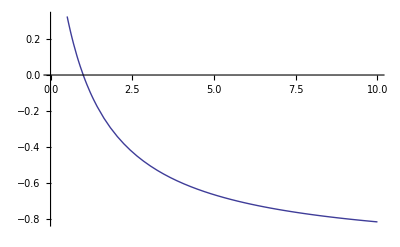

```mathematica
Plot[(1-b)/(1+b),{b,0,10}]
```

```mathematica
replacements2 = Table[HPL[LB⟦ii⟧,a]->HPLArgTransform[HPL[LB⟦ii⟧,b],b->-b,δ],{ii,Length[LB]}];
```

```mathematica
Save["negate_arguments.dat",replacements2]
```

```mathematica
$HPLAutoConvertToKnownFunctions=False
```

False

```mathematica
$HPLAutoReduceToMinimalSet=True
```

True

```mathematica
?HPLArgTransform
```

"HPLArgTransform[x,r,delta] transform the argument of the HPLs in x using the rule r. This rule has to be one of\n\nx->-x\n\nx->1-x\n\nx->√x\n\nx->x/(x-1)\n\nx->(1-x)/(1+x)\n\nx->1/x\n\nthe rule may be expressed in terms of any symbol. The argument delta is optional. It fixes whether the argument is in the upper (delta=+1) or in the lower (delta=-1) half complex plane. It can also be left symbolic. The default value for delta if it is omitted is $HPLAnalyticContinuationSign."

```mathematica
HPLArgTransform[HPL[{0,0,0,1},x],x->x/(x-1),δ]
```

-1/24 (HPL({1},x/(x-1)))^4-HPL({3},x/(x-1)) HPL({1},x/(x-1))-HPL({2,1},x/(x-1)) HPL({1},x/(x-1))+(HPL({2},x/(x-1)))^2-HPL({4},x/(x-1))-2 HPL({2,2},x/(x-1))+3/4 (2 HPL({2,2},x/(x-1))-(HPL({2},x/(x-1)))^2)+1/2 (-HPL({2},x/(x-1)) (HPL({1},x/(x-1)))^2+4 HPL({2,1},x/(x-1)) HPL({1},x/(x-1))-6 HPL({2,1,1},x/(x-1)))+2 HPL({2,1,1},x/(x-1))

```mathematica
generateLyndonBasis
```

```mathematica
-HPLArgTransform[HPL[{-1},x],x->(1-x)/(1+x),δ]+Log[2]
```

HPL({-1},(1-x)/(x+1))

```mathematica
Solve[x==(1+t)/(1-t),t]⟦1,1⟧
```

t→(x-1)/(x+1)

```mathematica
(x/2+1/2)/.(x->(1+τ)/(1-τ))//Simplify
```

1/(1-τ)

```mathematica
Solve[u==1/(1-τ),τ]
```

{{τ→(u-1)/u}}

```mathematica
HPL[{1},1-u]/.u->1/(1-τ)
```

HPL({1},1-1/(1-τ))

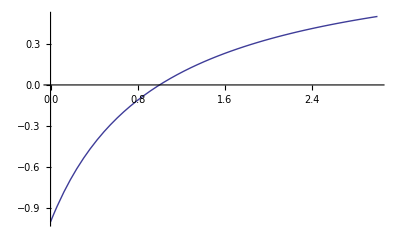

```mathematica
Plot[-(1-x)/(1+x),{x,0,3}]
```

```mathematica
$HPLAutoConvertToSimplerArgument=True
```

```mathematica
Expand[HPLArgTransform[HPL[{1,-1},x],x->(1-x)/(1+x),δ]+Log[2]^2/2-Zeta[2]/2-Log[2]^2-Log[2]HPLArgTransform[HPL[{1},x],x->(1-x)/(1+x),δ]]
```

HPL({-2},(1-x)/(x+1))-HPL({-1,-1},(1-x)/(x+1))-π^2/6

```mathematica
HPL[{0,1},τ/(τ-1)]+HPL[{0,1},τ]+HPL[{1},τ]^2/2-ζ[2]
```

1/2 (HPL({1},τ))^2+HPL({2},τ)+HPL({2},τ/(τ-1))-ζ(2)

```mathematica
1-u/.u->1/(1-τ)//Simplify
```

τ/(τ-1)

```mathematica
Solve[U==τ/(τ-1),τ]
```

{{τ→U/(U-1)}}

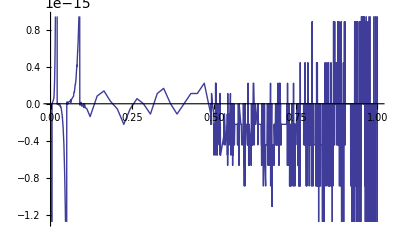

```mathematica
Plot[-HPL[{0,1},τ]-HPL[{1},τ]^2/2- HPL[{0,1},τ/(τ-1)],{τ,0,1}]
```

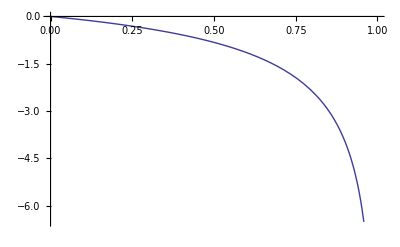

```mathematica
Plot[-HPL[{0,1},τ]-HPL[{1},τ]^2/2+0 Zeta[2],{τ,0,1}]
```

```mathematica
|
```

```mathematica
<<"invertArgument_8.mx";
```

```mathematica
flipArgument
```

```mathematica
Save["invertArgument_8.dat",invertArgument]
```